## Cross-sections for various processes

### Definitions

```mathematica
<<FeynCalc`;
vRel[m1_,m2_,p_]=(√(ScalarProduct[p1,p2]^2-m1^2*m2^2))/(√(p^2+m1^2)*√(p^2+m2^2))/.{ScalarProduct[p1,p2]->√(p^2+m1^2)√(p^2+m2^2)+p^2};
qSolArbitrary[m1_,m2_,m3_,m4_,p_]=q/.Solve[√(p^2+m1^2)+√(p^2+m2^2)==√(q^2+m3^2)+√(q^2+m4^2),q][[2]]//Simplify;
qSolEqualm1m2[m1_,m3_,m4_,p_]=Refine[Limit[qSolArbitrary[m1,m2,m3,m4,p],m2->m1],m1>0]//Simplify;
qSol[m1_,m2_,m3_,m4_]=If[m1/m2==1,Evaluate[qSolEqualm1m2[m1,m2,m3,m4,p],Evaluate[qSolEqualm1m2[m1,m3,m4,p]]]];
Ecm[p_,m1_,m2_]=√(p^2+m1^2)+√(p^2+m2^2);
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

### Pions

#### Importing matrix elements

```mathematica
Mπann=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology/matrix elements/Piannihilation.mx"}],"MX"]
Mπannπ0π0=Mπann[[1]];
Mπannγγ=Mπann[[2]]/.{e->√(4Pi*αEM)};
vrel=Refine[vRel[mπplus,mπplus,p]//Simplify,p>0];
ECM=Ecm[p,mπplus,mπplus]//Simplify;
PreFactorπAnn=1/((2*Pi)^2*4*ECM)1/(2*√(p^2+mπplus^2)*2*√(p^2+mπplus^2));
```

{(2 (OverBar[pπ02]·OverBar[pπ1])+2 (OverBar[pπ02]·OverBar[pπ2])+4 (OverBar[pπ1]·OverBar[pπ2])-mπ0^2+2 mπplus^2)/(3 fπ^2),2 e^2 (ε̄(pγ1)·ε̄(pγ2))}

#### π^+π^-->π^0 π^0

1/4 √((mπ0^4-8 mπplus^2 (2 mπ0^2-4 p^2)-2 mπ0^2 (mπ0^2+4 p^2)+(mπ0^2-4 p^2)^2+16 mπplus^4)/(mπplus^2+p^2))

Symbolic expression for σv in terms of the CM momentum p:

(√(-mπ0^2+mπplus^2+p^2) (mπ0^2-2 (5 mπplus^2+6 p^2))^2)/(576 π fπ^4 (mπplus^2+p^2)^(3/2))

((mπ0^2-10 mπplus^2)^2 √(mπplus^2-mπ0^2))/(576 π fπ^4 mπplus^3)

2.78842

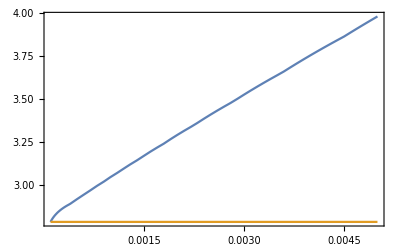

```mathematica
Mπann2=Mπannπ0π0^2/.{ScalarProduct[pπ1,pπ2]->(√(p^2+mπplus^2))^2+p^2,ScalarProduct[pπ01,pπ02]->(√(q^2+mπ0^2))^2+q^2,ScalarProduct[pπ1,pπ01]->√(p^2+mπplus^2)√(q^2+mπ0^2)-p*q*cosθ,ScalarProduct[pπ2,pπ02]->√(p^2+mπplus^2)√(q^2+mπ0^2)-p*q*cosθ,ScalarProduct[pπ1,pπ02]->√(p^2+mπplus^2)√(q^2+mπ0^2)+p*q*cosθ,ScalarProduct[pπ2,pπ01]->√(p^2+mπplus^2)√(q^2+mπ0^2)+p*q*cosθ}//Simplify;
qval=qSolEqualm1m2[mπplus,mπ0,mπ0,p]
IdenticalParticles=1/2;
dσvπdΩ["π^+","π^0"]=Refine[Refine[IdenticalParticles*PreFactorπAnn*qval*Mπann2//Expand//Simplify,q>0]/.{q->qval}//Simplify,mπplus>0];
Print["Symbolic expression for σv in terms of the CM momentum p:"]
σvAnn["π^+","π^0",p_]=Integrate[dσvπdΩ["π^+","π^0"],{cosθ,-1,1}]*2Pi
Refine[σvAnn["π^+","π^0",p]/.{p->0},mπplus>0]
σvAnn["π^+","π^0",p]/.{p->0}/.{mπplus->mass["π^+"],mπ0->mass["π^0"],fπ->fπv}
σvAnnπNum[p_]=σvAnn["π^+","π^0",p]/.{mπplus->mass["π^+"],mπ0->mass["π^0"],fπ->fπv};
σAnnπNum[s_]=Quiet[Refine[(σvAnnπNum[p]/vrel/.{p->(p/.Solve[2 √(p^2+mπplus^2)==√s,p][[2]])}//Simplify)/.{mπplus->mass["π^+"]},s>0]];
(*Thermal averaged cross-section: Eq. (A.68) from https://arxiv.org/pdf/2001.04466*)
Lambda[a_,b_,c_]=a^2+b^2+c^2-2*(a*b+b*c+a*c);
σvAnnπTaveraged[T_]:=If[T<3.9*10^-4,σvAnnπNum[0.],1/(8T mass["π^-"]^4*N[BesselK[2,mass["π^-"]/T]^2,$MachinePrecision])*NIntegrate[Rationalize[BesselK[1,Sqrt[s]/T] s^(3/2)Lambda[1,(mass["π^+"]^2)/s,(mass["π^+"]^2)/s]*σAnnπNum[s],0],{s,4*mass["π^-"]^2,Infinity},WorkingPrecision->20]]
σvAnnπTaveragedTab=ParallelTable[{T,Re[Quiet[σvAnnπTaveraged[T]]]},{T,Join[{10^-5.,2*10^-5.,5*10^-5.,8*10^-5.,10^-4.,3.9*10^-4.},Table[10^T,{T,Log10[4.5*10^-4],Log10[30*10^-3.],0.1}]]}];
σvAnn["π^+","π^0",T_]=Interpolation[Log[σvAnnπTaveragedTab],InterpolationOrder->1][Log[T]]//Exp;
Plot[{σvAnn["π^+","π^0",T],σvAnnπNum[0]},{T,10^-4.,5*10^-3.},Frame->True]
```

#### π^+π^-->2γ

```mathematica
M2πannγγ=DoPolarizationSums[DoPolarizationSums[Mπannγγ*ComplexConjugate[Mπannγγ],pγ1,0],pγ2,0]/.{ScalarProduct[pπ1,pπ2]->(√(p^2+mπplus^2))^2+p^2,ScalarProduct[pπ01,pπ02]->(√(q^2+mπ0^2))^2+q^2,ScalarProduct[pπ1,pπ01]->√(p^2+mπplus^2)√(q^2+mπplus^2)-p*q*cosθ,ScalarProduct[pπ2,pπ02]->√(p^2+mπplus^2)√(q^2+mπ0^2)-p*q*cosθ,ScalarProduct[pπ1,pπ02]->√(p^2+mπplus^2)√(q^2+mπ0^2)+p*q*cosθ,ScalarProduct[pπ2,pπ01]->√(p^2+mπplus^2)√(q^2+mπ0^2)+p*q*cosθ}//Simplify;
qval=qSolEqualm1m2[mπplus,0,0,p]//Simplify
IdenticalParticles=1/2;
dσvdΩ["π^+","γ"]=Refine[Refine[IdenticalParticles*PreFactorπAnn*qval*M2πannγγ//Expand//Simplify,q>0]/.{q->qval}//Simplify,mπplus>0]
σvAnnTemp["π^+","γ",p_]=Integrate[dσvdΩ["π^+","γ"],{cosθ,-1,1}]*2Pi
σvAnnSymbolic["π^+","γ"]=σvAnnTemp["π^+","γ",p]/.{p->0}
σvAnn["π^+","γ"]=σvAnnSymbolic["π^+","γ"]/.{mπplus->mass["π^+"],mπ0->mass["π^0"],fπ->fπv,αEM->1/137.}
σvAnnTot["π^+",T_]=σvAnnTot["π^-",T_]=σvAnn["π^+","π^0",T]+σvAnn["π^+","γ"];
σvAnn["π^+","μ^+"]=σvAnn["π^+","μ^-"]=σvAnn["π^-","μ^+"]=σvAnn["π^-","μ^-"]=0.;
```

√(mπplus^2+p^2)

αEM^2/(mπplus^2+p^2)

(4 π αEM^2)/(mπplus^2+p^2)

(4 π αEM^2)/mπplus^2

0.0346529

#### p<->n conversion cross-section

-Graphics-

```mathematica
xparZE[T_]=(2π*αEMv)/(√(T/mass["π^+"])+√(T/mass["p"]));
ZE[T_]=xparZE[T]/(1-Exp[-xparZE[T]]);
σvConv["π^-","p->n",T_]=σvNuclTot["π^-","p",T_]=m3sToGeVm2*4.3*10^-23. ZE[T];
σvConv["π^-","n->p",T_]=σvNuclTot["π^-","n",T_]=0;
σvConv["π^-","p->n",T]/ZE[T]
σvConv["π^+","n->p",T_]=σvNuclTot["π^+","n",T_]=1.1*σvConv["π^-","p->n",T]/ZE[T]
σvConv["π^+","p->n",T_]=σvNuclTot["π^+","p",T_]=0;

npπ[T_]=nBSBBN[T]*σvConv["π^-","p->n",T]/(σvConv["π^-","p->n",T]+σvConv["π^+","n->p",T]);
nnπ[T_]=nBSBBN[T]*σvConv["π^+","n->p",T]/(σvConv["π^-","p->n",T]+σvConv["π^+","n->p",T]);
```

3.58333

3.94167

### Muons

```mathematica
vrel=Refine[vRel[mμ,mμ,p]//Simplify,p>0];
ECM=Ecm[p,mμ,mμ]//Simplify;
PreFactorμAnn=1/((2*Pi)^2*4*ECM)1/(2*√(p^2+mμ^2)*2*√(p^2+mμ^2));
σvNuclTot["μ^+","p",T]=σvNuclTot["μ^+","n",T]=σvNuclTot["μ^-","p",T]=σvNuclTot["μ^-","n",T]=0.;
```

#### Annihilation into electrons

```mathematica
Mproc=(4Pi*αEM)*SpinorVBar[pμ1,mμ].GA[μ].SpinorU[pμ2,mμ](-MT[μ,ν])/ScalarProduct[pμ1+pμ2,pμ1+pμ2] SpinorVBar[pe1,me].GA[μ].SpinorU[pe2,me]//Contract//ExpandScalarProduct;
Mproc2=1/4 FermionSpinSum[Mproc*ComplexConjugate[Mproc]]/.DiracTrace->TR//Contract//Simplify//ExpandScalarProduct;
Mproc2=Mproc2/.{ScalarProduct[pe1,pe2]->(√(q^2+me^2))^2+q^2,ScalarProduct[pμ1,pμ2]->(√(p^2+mμ^2))^2+p^2,ScalarProduct[pμ1,pμ1]->mμ^2,ScalarProduct[pμ2,pμ2]->mμ^2}//Simplify;
qval=qSolEqualm1m2[mμ,me,me,p]//Simplify
dσvdΩ["μ^+","e^+"]=Refine[Refine[PreFactorμAnn*qval*Mproc2//Expand//Simplify,q>0]/.{q->qval}//Simplify,mμ>0];
σvAnnTemp["μ^+","e^+",p_]=Integrate[dσvdΩ["μ^+","e^+"],{cosθ,-1,1}]*2Pi
σvAnnSymbolic["μ^+","e^+"]=Normal@Series[σvAnnTemp["μ^+","e^+",p],{p,0,0},{me,0,0}]
σvAnn["μ^+","e^+"]=σvAnnSymbolic["μ^+","e^+"]/.{αEM->αEMv,mμ->mass["μ^+"]}
```

√(-me^2+mμ^2+p^2)

(π αEM^2 (3 mμ^2+2 p^2) √(-me^2+mμ^2+p^2) (me^2+2 (mμ^2+p^2)))/(2 (mμ^2+p^2)^(7/2))

(3 π αEM^2)/mμ^2

0.0455461

#### Annihilation into photons

```mathematica
ScalarProduct[pγ1,pγ1]=0;
ScalarProduct[pγ2,pγ2]=0;
Mproc11=(4Pi*αEM)/(ScalarProduct[pμ1-pγ1,pμ1-pγ1]-mμ^2)*SpinorVBar[pμ2,mμ].GA[ν].(GS[pμ1-pγ1]+mμ).GA[μ].SpinorU[pμ1,mμ]*PolarizationVector[pγ1,μ]*PolarizationVector[pγ2,ν]//Contract//ExpandScalarProduct;
Mproc12=(4Pi*αEM)/(ScalarProduct[pμ1-pγ2,pμ1-pγ2]-mμ^2)*SpinorVBar[pμ2,mμ].GA[μ].(GS[pμ1-pγ2]+mμ).GA[ν].SpinorU[pμ1,mμ]*PolarizationVector[pγ1,μ]*PolarizationVector[pγ2,ν]//Contract//ExpandScalarProduct;
Mproc2=1/4 DoPolarizationSums[DoPolarizationSums[FermionSpinSum[(Mproc11+Mproc12)*ComplexConjugate[(Mproc11+Mproc12)/.{α->α1}]],pγ1,0],pγ2,0]/.DiracTrace->TR//Contract//Simplify//ExpandScalarProduct;
Mproc2=Mproc2/.{ScalarProduct[pμ1,pμ2]->(√(p^2+mμ^2))^2+p^2,ScalarProduct[pγ1,pμ2]->√(p^2+mμ^2)*q+p*q*cosθ,ScalarProduct[pγ2,pμ1]->√(p^2+mμ^2)*q+p*q*cosθ,ScalarProduct[pμ1,pμ1]->mμ^2,ScalarProduct[pγ1,pγ1]->mγ^2,ScalarProduct[pγ2,pγ2]->mγ^2,ScalarProduct[pγ1,pμ1]->√(p^2+mμ^2)*q-p*q*cosθ,ScalarProduct[pγ2,pμ2]->√(p^2+mμ^2)*q-p*q*cosθ,ScalarProduct[pγ1,pγ2]->q^2+q^2}//Simplify;
qval=Refine[qSolEqualm1m2[mμ,0,0,p]//Simplify,mμ>0&&p>0]
IdenticalParticles=1/2;
dσvdΩ["μ^+","γ"]=Refine[Refine[IdenticalParticles*PreFactorμAnn*qval*Mproc2//Expand//Simplify,q>0]/.{q->qval}//Simplify,mμ>0];
σvAnn["μ^+","γ",p_]=Refine[((Integrate[dσvdΩ["μ^+","γ"],cosθ]/.{cosθ->1})-(Integrate[dσvdΩ["μ^+","γ"],cosθ]/.{cosθ->-1}))*2Pi//Simplify,p>0&&mμ>0]/.{p(-mμ^2-p^2)^(5/2)->p*I*(mμ^2+p^2)^(5/2)}
σvAnnSymbolic["μ^+","γ"]=Refine[Normal@Series[σvAnn["μ^+","γ",p],{p,0,0},{me,0,0}],mμ>0]
σvAnn["μ^+","γ"]=σvAnnSymbolic["μ^+","γ"]/.{αEM->αEMv,mμ->mass["μ^+"]}
σvAnnTot["μ^+",T_]=σvAnnTot["μ^-",T_]=σvAnn["μ^+","γ"]+σvAnn["μ^+","e^+"];
```

√(mμ^2+p^2)

-1/(p (-mμ^2-p^2)^(5/2))π αEM^2 (ⅈ p √(mμ^2+p^2) (2 mμ^2+p^2)-ⅈ (3 mμ^4+6 mμ^2 p^2+2 p^4) tanh^-1(p/(√(mμ^2+p^2))))

(π αEM^2)/mμ^2

0.015182

### Kaons

#### Importing matrix elements

```mathematica
{MK0annπ0π0,MK0annπpπm,MKpannπ0π0,MKpannπpπm}=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology/matrix elements/Kannihilation.mx"}],"MX"]
vrel=Refine[vRel[mK,mK,p]//Simplify,p>0];
ECM=Ecm[p,mK,mK]//Simplify;
PreFactorKAnn=1/((2*Pi)^2*4*ECM)1/(2*√(p^2+mK^2)*2*√(p^2+mK^2));
```

{1/(12 fπ^2 md)(4 md (OverBar[pK1]·OverBar[pK2])+2 md (OverBar[pK1]·OverBar[pπ2])+2 md (OverBar[pK2]·OverBar[pπ2])+2 md mK^2+md mπ0^2+mπ0^2 ms),1/(12 fπ^2 md)(4 md (OverBar[pK1]·OverBar[pK2])-4 md (OverBar[pK1]·OverBar[pπ2])+8 md (OverBar[pK2]·OverBar[pπ2])+2 md mK^2+md mπ0^2+mπ0^2 ms),1/(12 fπ^2 md)(4 md (OverBar[pK1]·OverBar[pK2])+2 md (OverBar[pK1]·OverBar[pπ2])+2 md (OverBar[pK2]·OverBar[pπ2])+2 md mK^2+md mπ0^2+mπ0^2 ms),1/(12 fπ^2 md)(4 md (OverBar[pK1]·OverBar[pK2])+8 md (OverBar[pK1]·OverBar[pπ2])-4 md (OverBar[pK2]·OverBar[pπ2])+2 md mK^2+md mπ0^2+mπ0^2 ms)}

#### Cross-sections

```mathematica
{MannSquared["K^0","π^0"],MannSquared["K^+","π^0"],MannSquared["K^0","π^+"],MannSquared["K^+","π^+"]}=(#^2/.{ScalarProduct[pK1,pK2]->(√(p^2+mK^2))^2+p^2,ScalarProduct[pπ1,pπ2]->(√(q^2+mπ^2))^2+q^2,ScalarProduct[pK1,pπ1]->√(p^2+mK^2)√(q^2+mπ^2)-p*q*cosθ,ScalarProduct[pK2,pπ2]->√(p^2+mK^2)√(q^2+mπ^2)-p*q*cosθ,ScalarProduct[pK1,pπ2]->√(p^2+mK^2)√(q^2+mπ^2)+p*q*cosθ,ScalarProduct[pK2,pπ1]->√(p^2+mK^2)√(q^2+mπ^2)+p*q*cosθ}/.{mπ0->mπ}//Simplify)&/@{MK0annπ0π0,MKpannπ0π0,MK0annπpπm,MKpannπpπm};
qvalK["K^0","π^0"]=qvalK["K^+","π^0"]=qvalK["K^0","π^+"]=qvalK["K^+","π^+"]=Refine[qSolEqualm1m2[mK,mπ,mπ,p]//Simplify,mK>0&&mπ>0&&p>0]
IdenticalParticlesK["K^0","π^0"]=IdenticalParticlesK["K^+","π^0"]=1/2;
IdenticalParticlesK["K^0","π^+"]=IdenticalParticlesK["K^+","π^+"]=1;
keysK=Keys[DownValues@qvalK][[All,1,#]]&/@{1,2}//Transpose;
Do[Module[{k,pi},
{k,pi}=keysK[[i]];
dσvdΩ[k,pi]=Refine[Refine[IdenticalParticlesK[k,pi]*PreFactorKAnn*q*MannSquared[k,pi]//Expand//Simplify,q>0]/.{q->qvalK[k,pi]}//Simplify,mπ>0&&mK>0];
σvAnn[k,pi,p_]=Integrate[dσvdΩ[k,pi],{cosθ,-1,1}]*2Pi//Simplify;
σvAnnSymbolic[k,pi]=Refine[Limit[σvAnn[k,pi,0],p->0]//Simplify,mK>0&&mπ>0];
σvAnn[k,pi]=σvAnnSymbolic[k,pi]/.{mK->mass["K^+"],mπ->mass["π^+"],md->mass["d"],ms->mass["s"],fπ->fπv}
]
,{i,1,Length[keysK],1}];
σvAnnSymbolic["K^+","π^0"]+σvAnnSymbolic["K^+","π^+"]//Simplify
σvAnn["K^+","π^-"]=σvAnn["K^-","π^-"]=σvAnn["K^-","π^+"]=σvAnn["K^+","π^+"];
σvAnn["K^+","μ^-"]=σvAnn["K^+","μ^+"]=σvAnn["K^-","μ^-"]=σvAnn["K^-","μ^+"]=σvAnn["K_L","μ^-"]=σvAnn["K_L","μ^+"]=σvAnn["K_S","μ^-"]=σvAnn["K_S","μ^+"]=0.;
σvAnn["K_L","π^+"]=σvAnn["K_L","π^-"]=σvAnn["K_S","π^+"]=σvAnn["K_S","π^-"]=σvAnn["K^0","π^+"];
σvAnnTot["K^+",T_]=σvAnnTot["K^-",T_]=σvAnn["K^+","π^0"]+σvAnn["K^+","π^+"]
σvAnnTot["K_L",T_]=σvAnnTot["K_S",T_]=σvAnn["K^0","π^0"]+σvAnn["K^0","π^+"]
{k,pi}//Clear
(*σvAnn["π^+","π^0",p]/.{p->0}
σvAnn["π^+","π^0",p]/.{p->0}/.{mπplus->mass["π^+"],mπ0->mass["π^0"],fπ->fπv}
σvAnnπNum[p_]=σvAnn["π^+","π^0",p]/.{mπplus->mass["π^+"],mπ0->mass["π^0"],fπ->fπv};
σvAnnπTaveragedTab=ParallelTable[{10^T,Quiet[NIntegrate[σvAnnπNum[p]*p^2*Exp[-p^2/(2*mass["π^+"]*10^T)],{p,0,100*10^T}]/NIntegrate[p^2*Exp[-p^2/(2*mass["π^+"]*10^T)],{p,0,100*10^T}]]},{T,-4.,Log10[40*10^-3.],0.02}];
σvAnn["π^+","π^0",T_]=Interpolation[σvAnnπTaveragedTab,InterpolationOrder->1][T];
Plot[{σvAnn["π^+","π^0",T],σvAnnπNum[0]},{T,10^-4.,5*10^-3.},Frame->True]*)
```

√(mK^2-mπ^2+p^2)

(√(mK^2-mπ^2) (md (10 mK^2+mπ^2)+mπ^2 ms)^2)/(3072 π fπ^4 md^2 mK^3)

44.2553

44.2553

#### Interaction with nucleons

Branching ratios of decays of resonances

```mathematica
(*Eq. 2.44 of https://arxiv.org/pdf/1006.4172*)
BrSM["Σ^+","p","π^+"]=BrSM["Σ^+","p","π^-"]=BrSM["Σ^+","n","π^-"]=0;
BrSM["Σ^+","n","π^+"]=0.483;
BrSM["Σ^+","p","π^0"]=1-BrSM["Σ^+","n","π^+"];
BrSM["Σ^-","p","π^+"]=BrSM["Σ^-","n","π^+"]=BrSM["Σ^-","p","π^-"]=0.;
BrSM["Σ^-","n","π^-"]=1.;
BrSM["Λ","p","π^+"]=BrSM["Λ","n","π^+"]=BrSM["Λ","n","π^-"]=0.;
BrSM["Λ","n","π^0"]=0.358;
BrSM["Λ","p","π^-"]=1-BrSM["Λ","n","π^0"];
BrSM["Σ^0","p","π^+"]=BrSM["Σ^0","n","π^+"]=BrSM["Σ^0","n","π^-"]=0.;
BrSM["Σ^0","p","π^-"]=BrSM["Λ","p","π^-"];
BrSM["Σ^0","n","π^0"]=BrSM["Λ","n","π^0"];
```

Partial cross-sections (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.37.3441)

```mathematica
σvNuclPartial["K^-","n","Σ^-","π^0"]=20mbToGeVm2;
σvNuclPartial["K^-","n","Σ^0","π^-"]=20mbToGeVm2;
σvNuclPartial["K^-","n","Λ","π^-"]=20mbToGeVm2;
σvNuclPartial["K^-","p","Σ^-","π^+"]=21*mbToGeVm2;
σvNuclPartial["K^-","p","Σ^+","π^-"]=9*mbToGeVm2;
σvNuclPartial["K^-","p","Σ^0","π^0"]=11*mbToGeVm2;
σvNuclPartial["K^-","p","Λ","π^0"]=4*mbToGeVm2;
```

Total cross-sections

```mathematica
(*Eq. 3.7 of https://journals.aps.org/prd/abstract/10.1103/PhysRevD.37.3441*)
xparZEK[T_]=(2π*αEMv)/(√(T/mass["K^+"])+√(T/mass["p"]));
ZEK[T_]=xparZEK[T]/(1-Exp[-xparZEK[T]]);
σvNuclTot["K^-","p",T_]=(σvNuclPartial["K^-","p","Σ^-","π^+"]+σvNuclPartial["K^-","p","Σ^+","π^-"]+σvNuclPartial["K^-","p","Σ^0","π^0"]+σvNuclPartial["K^-","p","Λ","π^0"])*ZEK[T];
σvNuclTot["K^-","p",T]/ZEK[T]
σvNuclTot["K^-","n",T_]=(σvNuclPartial["K^-","n","Σ^-","π^0"]+σvNuclPartial["K^-","n","Σ^0","π^-"]+σvNuclPartial["K^-","n","Λ","π^-"]);
σvNuclTot["K^-","n",T]
σvNuclTot["K_L","n",T_]=σvNuclTot["K_S","n",T_]=(7.+10.)mbToGeVm2;
σvNuclTot["K_L","n",T]
σvNuclTot["K_L","p",T_]=σvNuclTot["K_S","p",T_]=(7.+10.)mbToGeVm2;
σvNuclTot["K^+","p",T_]=σvNuclTot["K^+","n",T_]=0.;
```

112.5

150.

42.5

p<->n conversion cross-sections (https://journals.aps.org/prd/abstract/10.1103/PhysRevD.37.3441)

```mathematica
σvConv["K^-","n->p",T_]=(σvNuclPartial["K^-","n","Σ^-","π^0"]*(BrSM["Σ^-","p","π^-"]+BrSM["Σ^-","p","π^+"])+σvNuclPartial["K^-","n","Σ^0","π^-"]*(BrSM["Σ^0","p","π^-"])+σvNuclPartial["K^-","n","Λ","π^-"]*(BrSM["Λ","p","π^-"]));
σvConv["K^-","n->p",T]
σvConv["K^-","p->n",T_]=(σvNuclPartial["K^-","p","Σ^-","π^+"]*(BrSM["Σ^-","n","π^+"]+BrSM["Σ^-","n","π^-"])+σvNuclPartial["K^-","p","Σ^+","π^-"]*(BrSM["Σ^+","n","π^+"]+BrSM["Σ^+","n","π^-"])+σvNuclPartial["K^-","p","Σ^0","π^0"]*(BrSM["Σ^0","n","π^-"]+BrSM["Σ^0","n","π^+"]+BrSM["Σ^0","n","π^0"])+σvNuclPartial["K^-","p","Λ","π^0"]*(BrSM["Λ","n","π^+"]+BrSM["Λ","n","π^-"]+BrSM["Λ","n","π^0"]))*ZEK[T];
σvConv["K^-","p->n",T]/ZEK[T]
σvConv["K^+","n->p",T_]=σvConv["K^+","p->n",T_]=0.;
σvConv["K_L","n->p",T_]=σvConv["K_L","p->n",T_]=σvConv["K_S","n->p",T_]=σvConv["K_S","p->n",T_]=7.*mbToGeVm2;
```

64.2

76.7925

N->N cross-sections

```mathematica
(*For processes that do not convert nucleons*)
σvConv["K^-","n->n",T_]=(σvNuclPartial["K^-","n","Σ^-","π^0"]*(BrSM["Σ^-","n","π^-"]+BrSM["Σ^-","n","π^+"])+σvNuclPartial["K^-","n","Σ^0","π^-"]*(BrSM["Σ^0","n","π^-"]+BrSM["Σ^0","n","π^+"]+BrSM["Σ^0","n","π^0"])+σvNuclPartial["K^-","n","Λ","π^-"]*(BrSM["Λ","n","π^-"]+BrSM["Λ","n","π^+"]+BrSM["Λ","n","π^0"]));
σvConv["K^-","p->p",T_]=(σvNuclPartial["K^-","p","Σ^-","π^+"]*(BrSM["Σ^-","p","π^+"]+BrSM["Σ^-","p","π^-"])+σvNuclPartial["K^-","p","Σ^+","π^-"]*(BrSM["Σ^+","p","π^+"]+BrSM["Σ^+","p","π^-"]+BrSM["Σ^+","p","π^0"])+σvNuclPartial["K^-","p","Σ^0","π^0"]*(BrSM["Σ^0","p","π^-"]+BrSM["Σ^0","p","π^+"])+σvNuclPartial["K^-","p","Λ","π^0"]*(BrSM["Λ","p","π^+"]+BrSM["Λ","p","π^-"]))*ZEK[T];
σvConv["K^-","n->n",T]+σvConv["K^-","n->p",T]==σvNuclTot["K^-","n",T]
(σvConv["K^-","p->p",T]+σvConv["K^-","p->n",T])/ZEK[T]==σvNuclTot["K^-","p",T]/ZEK[T]
```

True

True

Fractions of π^(+/-) produced from overall interaction with nucleons

```mathematica
FractionπfromKnucl["K^-","n","π^-"]=1/σvNuclTot["K^-","n",T](σvNuclPartial["K^-","n","Σ^-","π^0"]*(BrSM["Σ^-","p","π^-"]+BrSM["Σ^-","n","π^-"])+σvNuclPartial["K^-","n","Σ^0","π^-"]*(1+BrSM["Σ^0","n","π^-"]+BrSM["Σ^0","p","π^-"])+σvNuclPartial["K^-","n","Λ","π^-"]*(1.+BrSM["Λ","n","π^-"]+BrSM["Λ","p","π^-"]));
FractionπfromKnucl["K^-","n","π^+"]=1/σvNuclTot["K^-","n",T](σvNuclPartial["K^-","n","Σ^-","π^0"]*(BrSM["Σ^-","p","π^+"]+BrSM["Σ^-","n","π^+"])+σvNuclPartial["K^-","n","Σ^0","π^-"]*(BrSM["Σ^0","n","π^+"]+BrSM["Σ^0","p","π^+"])+σvNuclPartial["K^-","n","Λ","π^-"]*(BrSM["Λ","n","π^+"]+BrSM["Λ","p","π^+"]));
FractionπfromKnucl["K^-","p","π^-"]=ZEK[T]/σvNuclTot["K^-","p",T](σvNuclPartial["K^-","p","Σ^-","π^+"]*(BrSM["Σ^-","p","π^-"]+BrSM["Σ^-","n","π^-"])+σvNuclPartial["K^-","p","Σ^+","π^-"]*(1+BrSM["Σ^+","p","π^-"]+BrSM["Σ^+","n","π^-"])+σvNuclPartial["K^-","p","Σ^0","π^0"]*(BrSM["Σ^0","n","π^-"]+BrSM["Σ^0","p","π^-"])+σvNuclPartial["K^-","p","Λ","π^0"]*(BrSM["Λ","n","π^-"]+BrSM["Λ","p","π^-"]));
FractionπfromKnucl["K^-","p","π^+"]=ZEK[T]/σvNuclTot["K^-","p",T](σvNuclPartial["K^-","p","Σ^-","π^+"]*(1+BrSM["Σ^-","p","π^+"]+BrSM["Σ^-","n","π^+"])+σvNuclPartial["K^-","p","Σ^+","π^-"]*(BrSM["Σ^+","p","π^+"]+BrSM["Σ^+","n","π^+"])+σvNuclPartial["K^-","p","Σ^0","π^0"]*(BrSM["Σ^0","n","π^+"]+BrSM["Σ^0","p","π^+"])+σvNuclPartial["K^-","p","Λ","π^0"]*(BrSM["Λ","n","π^+"]+BrSM["Λ","p","π^+"]));
(*For Subscript[K̄, L] - roughly - table 1 from https://journals.aps.org/prd/abstract/10.1103/PhysRevD.37.3441, where it is assumed that for all reactions 2 pions are produced, and nn/pp produce a half of π^-π^+ and a half of 2 π^0*)
FractionπfromKnucl["K_L","n","π^-"]=1/(7+10.)(7.*(1.)+10.*0.5*1);
FractionπfromKnucl["K_L","n","π^+"]=1/(7+10.)(7.*(0.)+10.*0.5*1);
FractionπfromKnucl["K_L","p","π^-"]=1/(7+10.)(7.*(0.)+10.*0.5*1);
FractionπfromKnucl["K_L","p","π^+"]=1/(7+10.)(7.*(1.)+10.*0.5*1);
Print["Whether the rates of disappearance of kaons respect the electric charge conservation: Q_Kσ_KN - (Q_(π^-)σ_(KN -> SuperscriptBox[π, -])+Q_(π^+)σ_(KN -> SuperscriptBox[π, +])) == (Q_N'-Q_N)σ_(KN -> N'). Here, σ_(KN -> SuperscriptBox[π, -]) == σ_(KN -> SuperscriptBox[π, -] + X)×<N_(π^-)>"]
Print["K^-+n->X:"]
(charge["K^-"]*σvNuclTot["K^-","n",T]-σvNuclTot["K^-","n",T]*(charge["π^-"]*FractionπfromKnucl["K^-","n","π^-"]+charge["π^+"]*FractionπfromKnucl["K^-","n","π^+"]))==(charge["p"]-charge["n"])*σvConv["K^-","n->p",T]
Print["K^-+p->X:"]
charge["K^-"]*σvNuclTot["K^-","p",T]-σvNuclTot["K^-","p",T]*(charge["π^-"]*FractionπfromKnucl["K^-","p","π^-"]+charge["π^+"]*FractionπfromKnucl["K^-","p","π^+"])==(charge["n"]-charge["p"])*σvConv["K^-","p->n",T]//Cancel
Print["K_L+n->X:"]
charge["K_L"]*σvNuclTot["K_L","p",T]-σvNuclTot["K_L","p",T]*(charge["π^-"]*FractionπfromKnucl["K_L","p","π^-"]+charge["π^+"]*FractionπfromKnucl["K_L","p","π^+"])==(charge["n"]-charge["p"])*σvConv["K_L","p->n",T]
Print["K_L+n->X:"]
charge["K_L"]*σvNuclTot["K^-","n",T]-σvNuclTot["K_L","n",T]*(charge["π^-"]*FractionπfromKnucl["K_L","n","π^-"]+charge["π^+"]*FractionπfromKnucl["K_L","n","π^+"])==(charge["p"]-charge["n"])*σvConv["K_L","n->p",T]
```

Whether the rates of disappearance of kaons respect the electric charge conservation: Q_Kσ_KN - (Q_(π^-)σ_(KN -> SuperscriptBox[π, -])+Q_(π^+)σ_(KN -> SuperscriptBox[π, +])) == (Q_N'-Q_N)σ_(KN -> N'). Here, σ_(KN -> SuperscriptBox[π, -]) == σ_(KN -> SuperscriptBox[π, -] + X)×<N_(π^-)>

K^-+n->X:

True

K^-+p->X:

True

K_L+n->X:

True

K_L+n->X:

True